#### Funkcija Houghove transformacije

```mathematica
HoughCircleDetection[image_Image,radiusmin_Integer: 1,radiusmax_Integer: 40,edgedetectradius_Integer: 10,minfitvalue_Real: .25,radiusstep_Integer: 1,minhoughvoxels_Integer: 4]:=Module[{edgeimage,hough3dbin,hough3dbinlabels,coords,arraydim},edgeimage=SelectComponents[DeleteBorderComponents[EdgeDetect[image,edgedetectradius,Method->"Canny"]],"EnclosingComponentCount",#==0&];
hough3dbin=DeleteSmallComponents[Image3D[ParallelMap[Binarize[Image@Divide[ListConvolve[#,ImageData@edgeimage,Ceiling[(Length@#)/2]],Total[#,2]],minfitvalue]&,Map[Function[{r},DiskMatrix[r]-ArrayPad[DiskMatrix[r-1],1]][#]&,Range[radiusmin,radiusmax,radiusstep]]]],minhoughvoxels];
hough3dbinlabels=MorphologicalComponents[hough3dbin];
coords=ParallelMap[Round[Mean[Position[hough3dbinlabels,#]]]&,Sort[Rest@Tally@Flatten@hough3dbinlabels,#1[[2]]>#2[[2]]&][[All,1]]];
arraydim=Rest@Dimensions[hough3dbinlabels];
(*Print["Radii: ",Max[radiusmin+coords[[All,1]]-2]];*)
{Max[radiusmin+coords[[All,1]]-2],
ParallelMap[Function[{level,offx,offy},ImageMultiply[image,Image@ArrayPad[DiskMatrix[radiusmin+level-1],{{offx-radiusmin-level,First@arraydim-offx-radiusmin-level+1},{offy-radiusmin-level,Last@arraydim-offy-radiusmin-level+1}}]]][Sequence@@#]&,coords]}]
```

Uvoz slik

```mathematica
{FileNameSetter[Dynamic[f], "Directory"], Dynamic[f]}
```

{$CellContext`fDirectoryAll,}

```mathematica
files=FileNames["*.jpg",f];
all=Import[#]&/@files;
frejmi=Table[ImageCrop[all[[i]]],{i,Length[all]}];
```

-Graphics-

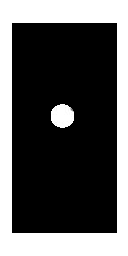

-Graphics-

```mathematica
ms=frejmi[[30]];
markschulzeedges=EdgeDetect[ms,10,Method->"Canny"]
ParallelMap[Image@Divide[ListConvolve[#,ImageData@markschulzeedges,Ceiling[(Length@#)/2]],Total[#,2]]&,Map[Function[{r},DiskMatrix[r]-ArrayPad[DiskMatrix[r-1],1]][#]&,Range[14,18,1]]];

j=Show[ImageApply[Plus,HoughCircleDetection[#,8,50,7,.30][[2,1]]],ImageSize->ImageDimensions[#]]&[ms]

X=ComponentMeasurements[j,{"Centroid","EquivalentDiskRadius"},#AdjacentBorderCount==0&&400<#Area<50000&];
HighlightImage[ms,Circle@@@X[[All,2]]]
```

#### Preverjanje

```mathematica
img2=ms;
measurementCircle[Dynamic[center_],Dynamic[r_]]:={Red,Thick,Dynamic@Circle[center,r],
Dynamic@
Text[Style[StringJoin[ToString@Round@r,"px"],FontSize->18],Scaled@{0.1,0.9},Background->RGBColor[0,0,0,0.5]]};

DynamicModule[
{center=ImageDimensions[img2]/2,r},Manipulate[
EventHandler[
DynamicImage[
img2,
Epilog->measurementCircle[Dynamic[center],Dynamic[r]]
],{"MouseDown":>If[CurrentValue["OptionKey"],center=MousePosition["Graphics"]]},PassEventsDown->Dynamic[Not[CurrentValue["OptionKey"]]]
],
{{r,32},8,800},
FrameMargins->0
]
]
```

```mathematica
korak=15;
Timing[R=Table[If[HoughCircleDetection[frejmi[[i]],8,50,7,.30][[1]]==-∞,0,HoughCircleDetection[frejmi[[i]],8,50,7,.30][[1]]],{i,1,Length[frejmi],korak}];]
```

{18.625,Null}

```mathematica
pxmmraz=0.18/(2 √2);

Rt=Table[{10^-6(i-1)3.3333 korak ,R[[i]] pxmmraz},{i,Length[R]}];
Rp={0,21,28,33,37,39,40,41,42,43,43,41,41,40,37,33,28,21,8,8,9,10} ;
Rtp=Table[{10^-6(i-1)3.333 10 ,Rp[[i]]pxmmraz},{i,Length[Rp]}];
Rpyt=Import["C:\\Users\\Jure Podobnikar\\Desktop\\Diploma\\Algoritmi\\Python\\test.txt","Table"]//Flatten;
Rpyt[[{1,2,3,4,5,6,7}]]={0,5,7,9,13,15,18};
Rtpyt=Table[{10^-6(i-1)3.3333 5 ,Rpyt[[i]]pxmmraz},{i,Length[Rpyt]}]
```

{{0.,0.},{0.0000166665,0.318198},{0.000033333,0.445477},{0.0000499995,0.572756},{0.000066666,0.827315},{0.0000833325,0.954594},{0.000099999,1.14551},{0.000116665,1.46371},{0.000133332,1.59099},{0.000149999,1.65463},{0.000166665,1.78191},{0.000183332,1.84555},{0.000199998,1.97283},{0.000216664,2.03647},{0.000233331,2.10011},{0.000249998,2.16375},{0.000266664,2.22739},{0.000283331,2.29103},{0.000299997,2.29103},{0.000316664,2.35467},{0.00033333,2.41831},{0.000349996,2.41831},{0.000366663,2.48194},{0.000383329,2.54558},{0.000399996,2.54558},{0.000416663,2.60922},{0.000433329,2.67286},{0.000449995,2.67286},{0.000466662,2.67286},{0.000483329,2.7365},{0.000499995,2.7365},{0.000516662,2.7365},{0.000533328,2.7365},{0.000549995,2.80014},{0.000566661,2.80014},{0.000583328,2.80014},{0.000599994,2.80014},{0.000616661,2.7365},{0.000633327,2.7365},{0.000649993,2.7365},{0.00066666,2.67286},{0.000683327,2.67286},{0.000699993,2.67286},{0.00071666,2.60922},{0.000733326,2.60922},{0.000749993,2.54558},{0.000766659,2.48194},{0.000783325,2.48194},{0.000799992,2.41831},{0.000816658,2.35467},{0.000833325,2.29103},{0.000849992,2.22739},{0.000866658,2.10011},{0.000883325,2.03647},{0.000899991,1.90919},{0.000916658,1.78191},{0.000933324,1.71827},{0.000949991,1.52735},{0.000966657,1.33643},{0.000983323,1.08187},{0.00099999,0.763675},{0.00101666,0.827315},{0.00103332,0.763675},{0.00104999,0.763675},{0.00106666,1.08187},{0.00108332,1.08187},{0.00109999,1.14551},{0.00111666,1.20915},{0.00113332,1.27279},{0.00114999,1.27279},{0.00116666,1.33643},{0.00118332,1.33643},{0.00119999,1.40007},{0.00121665,1.40007},{0.00123332,1.40007},{0.00124999,1.40007},{0.00126665,1.33643},{0.00128332,1.33643},{0.00129999,1.33643},{0.00131665,1.27279},{0.00133332,1.20915},{0.00134999,1.14551},{0.00136665,1.08187},{0.00138332,1.01823},{0.00139999,0.954594},{0.00141665,0.890955},{0.00143332,0.827315},{0.00144999,0.827315},{0.00146665,0.890955},{0.00148332,0.954594},{0.00149999,0.954594},{0.00151665,1.01823},{0.00153332,1.08187},{0.00154998,1.14551},{0.00156665,1.14551},{0.00158332,1.08187},{0.00159998,1.14551},{0.00161665,1.08187},{0.00163332,1.08187},{0.00164998,1.08187},{0.00166665,1.01823},{0.00168332,0.827315},{0.00169998,0.890955},{0.00171665,0.890955},{0.00173332,0.827315},{0.00174998,0.954594},{0.00176665,1.01823},{0.00178332,0.827315},{0.00179998,1.01823},{0.00181665,1.01823},{0.00183332,1.01823},{0.00184998,1.08187},{0.00186665,0.890955},{0.00188331,1.01823},{0.00189998,1.01823},{0.00191665,1.08187},{0.00193331,1.01823}}

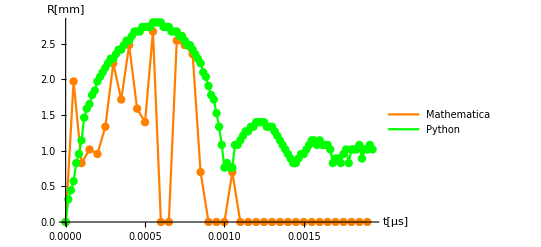

```mathematica
p1=ListLinePlot[Rt,AxesLabel->{"t[μs]","R[mm]"},PlotStyle->Orange,Mesh->All,PlotLegends->{"Mathematica"}];
p2=ListLinePlot[Rtp,AxesLabel->{"t[μs]","R[mm]"},PlotStyle->Blue,Mesh->All,PlotLegends->{"Ročno"}];
p3=ListLinePlot[Rtpyt,AxesLabel->{"t[μs]","R[mm]"},PlotStyle->Green,Mesh->All,PlotLegends->{"Python"}];
Show[p1,p3,PlotRange->All,ImageSize->Full]
```

```mathematica
Print["Odstopanje v Mathematici je ",N[Total[Table[{Abs[R[[i]]-Rp [[i]]]},{i,1,Length[Rp]}]//Flatten]/Length[Rp] pxmmraz,1],"mm."]
Print["Odstopanje v Pythonu je ",NumberForm[N[Total[Table[{Abs[Rpyt[[i]]-Rp [[i]]]},{i,1,Length[Rp]}]//Flatten]/Length[Rp] pxmmraz],1],"mm."]
```

Odstopanje v Mathematici je 4.mm.

Odstopanje v Pythonu je 5.mm.

```mathematica
Vhodni podatki
```

```mathematica
Tinf1=Quantity[293.15,"Kelvins"] (*Temperatura vode*)
Tinf=QuantityMagnitude[Tinf1];

pv1=Quantity[Exp[20.386-5132/Tinf]133.322368,"Pascals"](*Tlak nasičenja*)
pv=QuantityMagnitude[pv1];

σ1=Quantity[7.28 10^-2,"Newtons"/"Meters"](*Površinska napetost*)
σ=QuantityMagnitude[σ1];

R01=Quantity[2 10^-4,"Meters"](*Začetni polmer mehurčka*)
R0=QuantityMagnitude[R01];

ρl1=ThermodynamicData["Water","Density",{"Pressure"->Quantity[1000,"Millibars"],(*Gostota vode v kapljevinastem stanju*)"Temperature"->Quantity[QuantityMagnitude[Tinf],"Kelvins"]}]
ρl=QuantityMagnitude[ρl1];

ρv1=ThermodynamicData["Water","Density",{"Temperature"->Quantity[101,"DegreesCelsius"]}](*Gostota vodne pare*)
ρv=QuantityMagnitude[1.2];

η1=ThermodynamicData["Water","Viscosity",{"Pressure"->Quantity[1000,"Millibars"],"Temperature"->Quantity[Tinf,"Kelvins"]}](*Viskoznost vode*)
η=QuantityMagnitude[η1];

cpl1=ThermodynamicData["Water","IsobaricHeatCapacity",{"Pressure"->Quantity[1000,"Millibars"],"Temperature"->Quantity[QuantityMagnitude[Tinf],"Kelvins"]}]
(*Specifična izobarna toplotna kapacitivnost*)
cpl=QuantityMagnitude[cpl1];

γ=1.4(*Razmerje specifičnih toplot*)

λl1=ThermodynamicData["Water","ThermalConductivity",{"Pressure"->Quantity[1000,"Millibars"],"Temperature"->Quantity[Tinf,"Kelvins"]}]
λl=QuantityMagnitude[λl1];

L1=Quantity[2256.9 10^3,"J/kg"]
L=QuantityMagnitude[L1];

t01=Quantity[2 10^-3,"Seconds"]
t0=QuantityMagnitude[t01];

Thermo=0;
```

293.15 K

2374.1 Pa

0.0728 N/m

1/5000 m

998.207 kg/m^3

0.595884 kg/m^3

0.0010016 s Pa

4184.06 J/(kg K)

1.4

0.598461 W/(m K)

2.2569×10^6 J/kg

1/500 s

```mathematica
Robni pogoji
```

```mathematica
ω1=Quantity[23.4 10^3,"Hertz"](*Frekvenca*)
ω=QuantityMagnitude[ω1];

p01=Quantity[1.01 10^5,"Pascals"](*Začetni okoliški tlak*)
p0=QuantityMagnitude[p01];

pf1=Quantity[1 1.28 10^5,"Pascals"](*Vzbujalni tlak*)
pf=QuantityMagnitude[pf1];

pg01=p01-pv1+(2σ1)/R01
pg0=QuantityMagnitude[pg01];

αl1=λl1/(ρl 1cpl1)
αl=QuantityMagnitude[αl1];

sum1=(ρv1 L1)^2/(ρl1^2 cpl1 Tinf1 √αl1)Thermo;
sum=(ρv L)^2/(ρl^2 cpl Tinf √αl)Thermo

pinf[t_]=p0-pf Sin[2 π ω t]
```

23400. Hz

101000. Pa

128000. Pa

171426. N/m^2

1.43291×10^-7 kg W/(m J)

0.

101000.-128000. Sin[147027. t]

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Clear[pf,ω]
solns=ParametricNDSolveValue[{r''[t]==1/(ρl r[t]) (-(3(r'[t])^2)/2 ρl-r'[t] sum √t ρl+pv-p0+pf Sin[2 π ω t]+pg0 (R0^3/r[t]^3)^γ-2 σ/r[t]-4 η r'[t]/r[t]),r[0]==R0,r'[0]==0},{r},{t,0,t0},{pf,ω},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},MaxStepSize->2 10^-8];
```

```mathematica
Manipulate[Plot[Evaluate@Through[solns[pf,ω][t]],{t,0,a t0}],{{pf,0,"Vzbujevalni tlak"},0,10 10^6,Appearance->"Labeled"},{{ω,0,"Vzbujevalna frekvenca"},0,2 10^3,Appearance->"Labeled"},{{a,0.1,"Prikaz"},0,1.,Appearance->"Labeled"}]
```

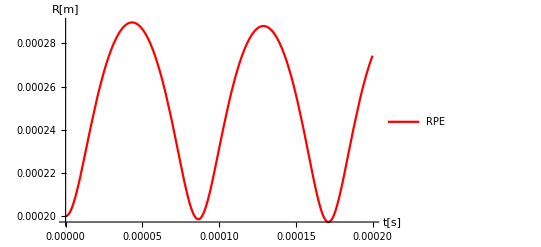

```mathematica
s3=NDSolve[{r''[t]==1/(ρl r[t]) (-(3(r'[t])^2)/2 ρl-r'[t] sum √t ρl+pv-p∞[t]+pg0 (R0/r[t])^(3γ)-2 σ/r[t]-4 η r'[t]/r[t]),r[0]==R0,r'[0]==0},r,{t,0,t0},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},MaxStepSize->2 10^-8];

r3[t_]=r[t]/.s3[[1]];
p4=Plot[r3[t],{t,0,0.1t0},AxesLabel->{"t[s]","R[m]"},AxesLabel->{"t[μs]","R[px]"},PlotStyle->Red,PlotLegends->{"RPE"}];
Show[p4,PlotRange->All,ImageSize->Full]
```

```mathematica
Clear[R0,pg0]
pg0=p0-pv+(2σ)/R0
pinf[t_]=p0-pf Sin[2 π ω t]
Rmax=6.08112 10^-3
tmax=(0.00074997+0.0008333)/2
```

98625.9+0.1456/R0

101000.-pf Sin[2 π t ω]

0.00608112

0.000791635

```mathematica
NSolve[0==1/(ρl Rmax)(pv-pinf[tmax]+pg0(R0^3/Rmax^3)^γ-(2σ)/Rmax),R0]
```

{{R0→-0.00822103+0.0142386 ⅈ},{R0→-0.00822103-0.0142386 ⅈ},{R0→0.016441}}

{{R0→-0.003-0.00519615 ⅈ},{R0→-0.003+0.00519615 ⅈ},{R0→0.006}}

98662

```mathematica
Solve[101000-2338==0.837 ρl x^2/0.0026^2]
```

{{x→-0.0282537},{x→0.0282537}}

```mathematica
(2π)/0.000150
```

41887.9

```mathematica
(3 5500 10^-6 60^2)/(8 π(2 10^-6))0.30
```

354518.

```mathematica
((1.83 10.88 10^-3 √(ρl/p0))/(2 π))^-1
```

3174.32

```mathematica
sin=Interpolation[Rtpyt]
```

InterpolatingFunction[{{0., 0.00218331}}, <>]

```mathematica
Fit[Rtpyt,{1,x,x^2,x^3,x^4,x^5},x]
```

3.87642+31706.6 x-4.51014×10^7 x^2+1.23528×10^10 x^3+5.87773×10^12 x^4-2.35835×10^15 x^5

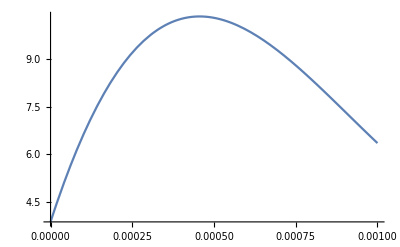

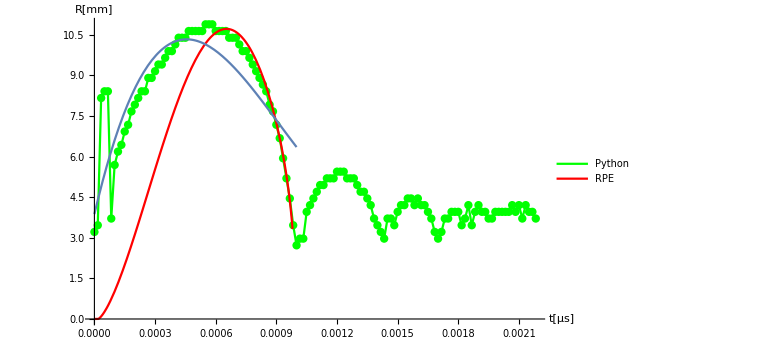

```mathematica
p5=Plot[%,{x,0,0.001}]
Show[p3,p4,p5,PlotRange->All,ImageSize->Large,PlotRange->All]
```

```mathematica
p∞[t_]=p0-3/(8 π) (6800 10^-6 60 Exp[-t/(0.139 6800 10^-6)])/(2 10^-6)
```

101000.-(76500 ⅇ^(-1057.98 t))/π

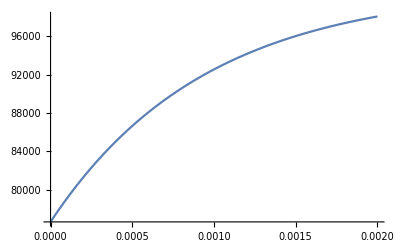

```mathematica
Plot[p∞[t],{t,0,t0}]
```

```mathematica
Solve[0.001==0.915 r0 √(ρl/(p0-pv))]
```

{{r0→0.0108634}}

```mathematica
ω0=√(3γ pg0/(ρl R0^2)-(2σ)/(ρl R0^3))
```

134216.